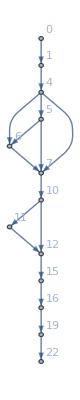

```mathematica
nums = DirectedGraph[{0 -> 1,
1 -> 4,
4 -> 5,
4 -> 6,
4 -> 7,
5 -> 6,
5 -> 7,
6 -> 7,
7 -> 10,
10 -> 11,
10 -> 12,
11 -> 12,
12 -> 15,
15 -> 16,
16 -> 19,
19 -> 22}, VertexLabels -> "Name"]
```

```mathematica
Length[FindPath[nums, 0, 19, Infinity, All]]
```

8